```mathematica
(* parameters *)
R=1 ;
L=2;
L2=3;
ω=1;
ϕ=-Pi/3;
T=2*Pi/ω;
timestop=2*Pi;
dt=0.01;
```

```mathematica
(* set right edge offset *)
maxX=R+L+L2;
minX=L+L2-R;
Reduce[(minX<=(-R+offset))&&((R+offset)<=maxX),{offset}]
```

offset==5

```mathematica
M=5;
```

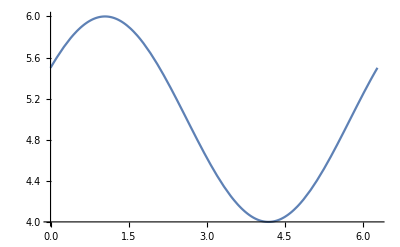

```mathematica
(* dependance between right edge of the rod and time *)
x1[t_]:=R*Cos[ω*t+ϕ]+M;
Plot[x1[t],{t,0,timestop}]
```

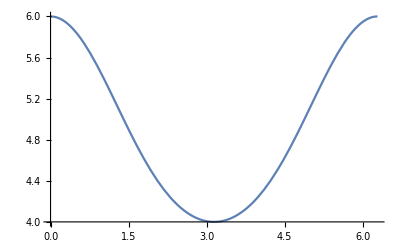

```mathematica
(* dependance between right edge of the rod and rotation angle phi *)
x2[p_]:=Cos[p]*R+Sqrt[L2^2-(Sin[p]*R)^2]+L;
Plot[x2[p],{p,0,2*Pi}]
```

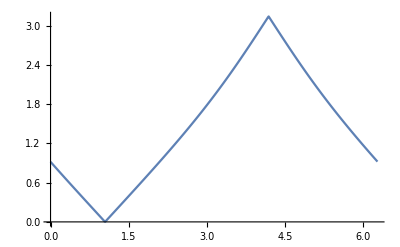

```mathematica
(* find and plot a dependance between rotation angle phi and time *)
phi=Table[FindRoot[x1[t]==x2[p],{p,1}][[1,2]],{t,0,timestop,dt}];
times=Range[0,timestop,dt];
ListLinePlot[Table[{times[[i]],phi[[i]]},{i,1,Length[times]}]]
```

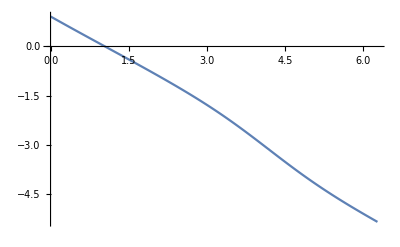

```mathematica
(* crutch *)
(* instead of turning,the flywheel moves in the other direction *)
minPhiIndex=Position[phi,Min[phi]][[1,1]];
maxPhiIndex=Position[phi,Max[phi]][[1,1]];
For[i=1, i<=Length[phi],  i++, If[i>=minPhiIndex&&i<=maxPhiIndex, phi[[i]]= -phi[[i]],If[i>=maxPhiIndex,phi[[i]]=phi[[i]]-2*Pi]];]
ListLinePlot[Table[{times[[i]],phi[[i]]},{i,1,Length[times]}]]
```

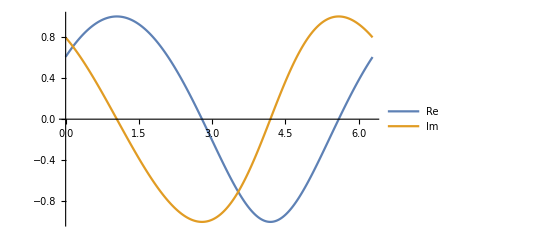

```mathematica
(* plot the exp(i*phi(t)) *)
expphi=Exp[I*phi];
ListLinePlot[{Re[expphi],Im[expphi]},PlotLegends->{"Re", "Im"} ,DataRange->{0,2*Pi}]
```

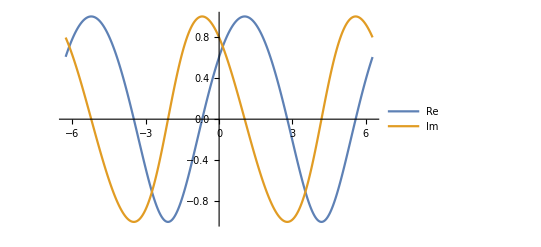

```mathematica
(* extend the func *)
expphi2=Join[Table[{-times[[Length[times]+1-i]],expphi[[i]]},{i,1,Length[times]}],Table[{times[[i]],expphi[[i]]},{i,1,Length[times]}]];
ListLinePlot[{Re[expphi2], Map[{#[[1]], Im[ #[[2]]]} &, expphi2]},PlotLegends->{"Re", "Im"}]
```

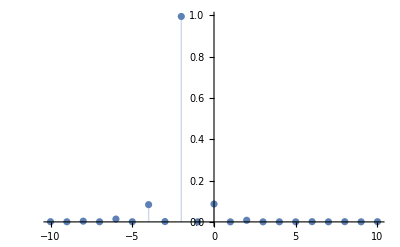

```mathematica
(* Fourier coefficients *)
numberOfCoeffs= 10;
fourierCoeffs = Association[Table[i->1/(2T)Total[Map[#[[2]] Exp[-I Pi i  (#[[1]])/T]dt &, expphi2]],{i, -numberOfCoeffs,numberOfCoeffs}]];
ListPlot[fourierCoeffs //Abs, PlotRange->All, Filling->Axis]
```